```mathematica
ClearAll["Global`*"]
```

```mathematica
L=1;
ys[x_]:={Cos[2 π x/L],Sin[2 π x /L]}
```

```mathematica
(*check for u[[1]]*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/dynamics/lagrangian_approach/one_dimension/circle/solution/nodal_values/ys.csv"][[2;;]];
t=Table[{t[[i,4]],t[[i,1]]},{i,2,Length[t]}]
```

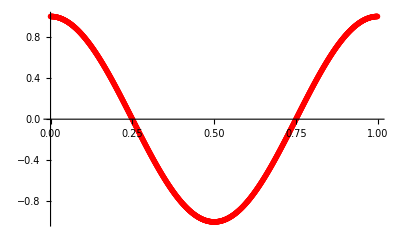

```mathematica
plotnum=ListPlot[t,PlotStyle->{Red,PointSize->0.01}]
```

```mathematica
(*check for u[[2]]*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/dynamics/lagrangian_approach/one_dimension/circle/solution/nodal_values/ys.csv"][[2;;]];
t=Table[{t[[i,4]],t[[i,2]]},{i,2,Length[t]}]
```

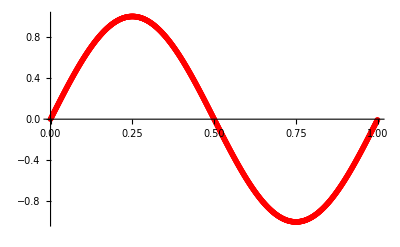

```mathematica
plotnum=ListPlot[t,PlotStyle->{Red,PointSize->0.01}]
```

```mathematica
(*plot normal vector*)
```

```mathematica
ys=Import["/Users/michelecastellana/Documents/finite_elements/dynamics/lagrangian_approach/one_dimension/circle/solution/nodal_values/ys.csv"][[2;;]];
u=Import["/Users/michelecastellana/Documents/finite_elements/dynamics/lagrangian_approach/one_dimension/circle/solution/snapshots/csv/nodal_values/u_n_9001.csv"][[2;;]];
```

```mathematica
(*points for the vector field*)
```

```mathematica
X=Table[{ys[[i,1]]+u[[i,1]],ys[[i,2]]+u[[i,2]]},{i,1,Length[u]}]
```

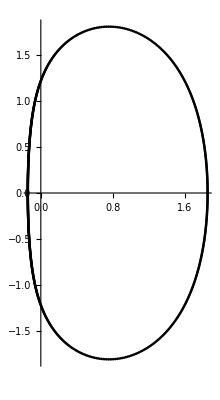

```mathematica
ListPlot[X,AspectRatio->Automatic,PlotStyle->Black]
```